```mathematica
ClearAll;
Read in Einstein oscillator potential ab initio data;
(*zrEinsteinmeV=26.329538754361874/1000;cEinsteinmeV=65.1879672429008/1000;*)
(*Carbon and Zironcium mass*)
m={12.0107,91.224,1};
kB=8.6173324*10^-3;
(*Data in*)SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Einstein_oscillator_4685Ang_ZrC"];
(*OLD input files :filesEinsteinPot={"C_300_1900_3200K_energy_displacment","C_300_1900_32e00K_energy_displacement_harmonic"};*)
filesEinsteinPot={"C_3200K_energy_displacement","C_3200K_energy_displacement_harmonic","Zr_3200K_energy_displacement","Zr_3200K_energy_displacement_harmonic"};
CarbonPotentialEinstein=ReadList[filesEinsteinPot[[1]],{Number, Number}];
cPlotData=ReadList[filesEinsteinPot[[1]],{Number, Number}];
CarbonPotentialEinsteinHarmonic=ReadList[filesEinsteinPot[[2]],{Number, Number}];
Show@ListPlot[CarbonPotentialEinstein,PlotLabel->"Anharmonic single Einstein oscillator potential for C in ZrC",AxesLabel->{"Displacement (Å)","Energy (meV)"}];
Show@ListPlot[CarbonPotentialEinsteinHarmonic,PlotLabel->"Harmonic single Einstein oscillator potential for C in ZrC",AxesLabel->{"Displacement (Å)","Energy (meV)"}];
ZirconPotentialEinstein=ReadList[filesEinsteinPot[[3]],{Number, Number}];
zPlotData=ReadList[filesEinsteinPot[[3]],{Number, Number}];
ZirconPotentialEinsteinHarmonic=ReadList[filesEinsteinPot[[4]],{Number, Number}];
Show@ListPlot[ZirconPotentialEinstein,PlotLabel->"Anharmonic single Einstein oscillator potential for Zr in ZrC",AxesLabel->{"Displacement (Å)","Energy (meV)"}];
Show@ListPlot[ZirconPotentialEinsteinHarmonic,PlotLabel->"Harmonic single Einstein oscillator potential for Zr in ZrC",AxesLabel->{"Displacement (Å)","Energy (meV)"}];
```

```mathematica
Define and fit potentials;
(*Carbon*)
V[1,2,x_]:=Fit[CarbonPotentialEinsteinHarmonic,{x^2},x]
V[1,4,x_]:=Fit[CarbonPotentialEinstein,{x^2,x^4},x]
V[1,6,x_]:=Fit[CarbonPotentialEinstein,{x^2,x^4,x^6},x]
V[1,8,x_]:=Fit[CarbonPotentialEinstein,{x^2,x^4,x^6,x^8},x]
V[1,10,x_]:=Fit[CarbonPotentialEinstein,{x^2,x^4,x^6,x^8,x^10},x]
V[1,12,x_]:=Fit[CarbonPotentialEinstein,{x^2,x^4,x^6,x^8,x^10,x^12},x]
(*Zirconium*)
V[2,2,x_]:=Fit[ZirconPotentialEinsteinHarmonic,{x^2},x]
V[2,4,x_]:=Fit[ZirconPotentialEinstein,{x^2,x^4},x]
V[2,6,x_]:=Fit[ZirconPotentialEinstein,{x^2,x^4,x^6},x]
V[2,8,x_]:=Fit[ZirconPotentialEinstein,{x^2,x^4,x^6,x^8},x]
V[2,10,x_]:=Fit[ZirconPotentialEinstein,{x^2,x^4,x^6,x^8,x^10},x]
V[2,12,x_]:=Fit[ZirconPotentialEinstein,{x^2,x^4,x^6,x^8,x^10,x^12},x]
```

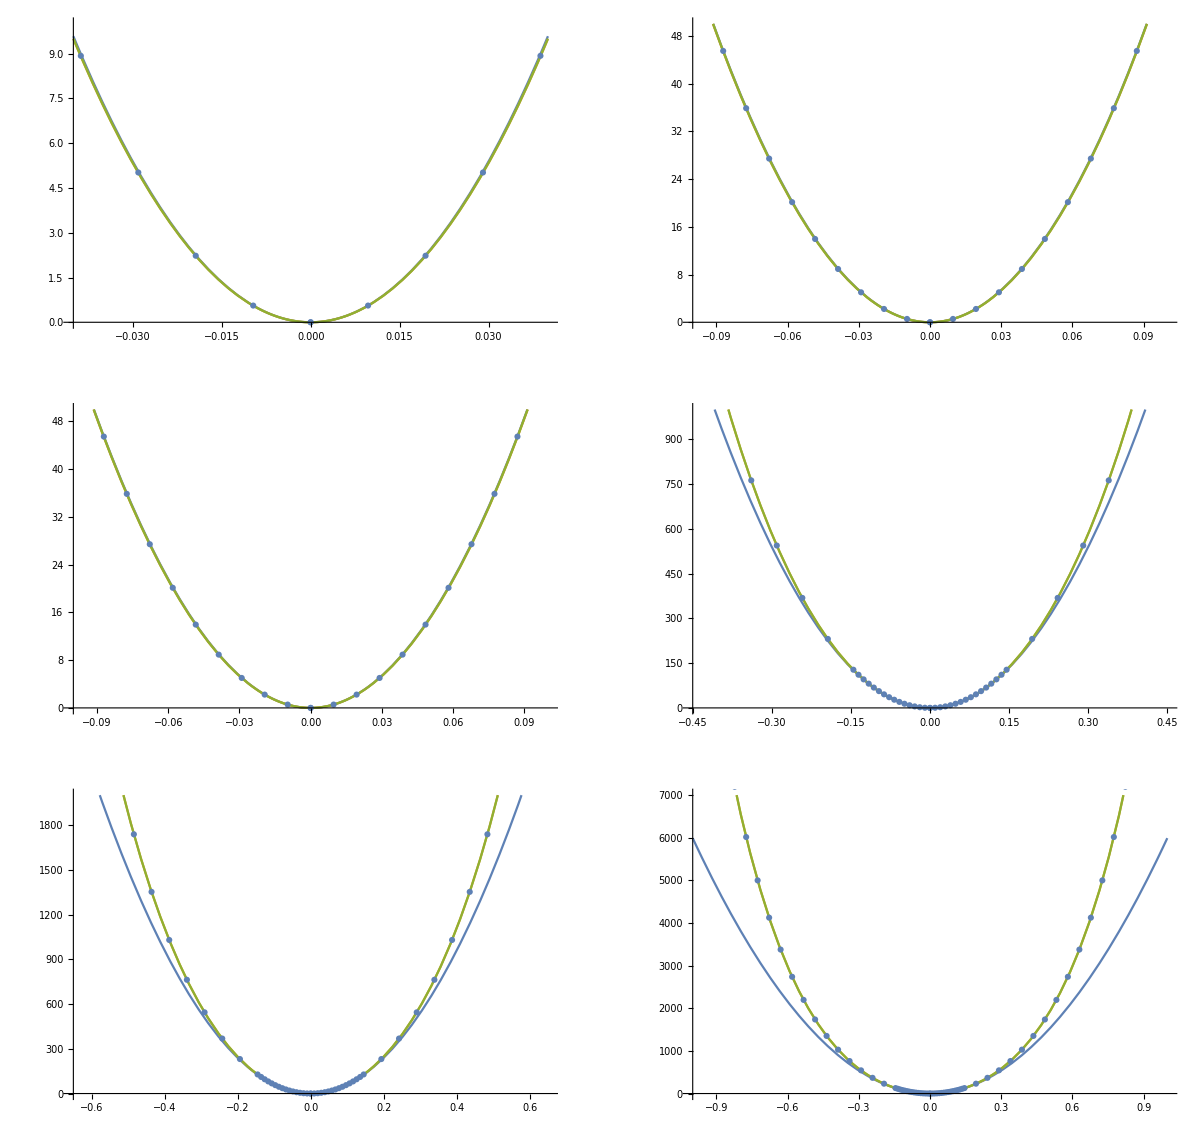

```mathematica
Carbon- look at the fits to examine agreement different length scales;
commonplotinfo={AxesLabel->{"Displacement (Å)","E-E0ref (meV) "}};
P00=With[{B=0.04,H=10},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,6,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P0=With[{B=0.1,H=50},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,6,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P1=With[{B=0.1,H=50},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,6,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P2=With[{B=0.45,H=1000},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,6,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P3=With[{B=0.65,H=2000},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,6,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P4=With[{B=1,H=7000},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,6,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
GraphicsGrid[{{Show[P00,ListPlot@cPlotData],Show[P0,ListPlot@cPlotData]},{Show[P1,ListPlot@cPlotData],Show[P2,ListPlot@cPlotData]},{Show[P3,ListPlot@cPlotData],Show[P4,ListPlot@cPlotData]}},ImageSize->1200]
```

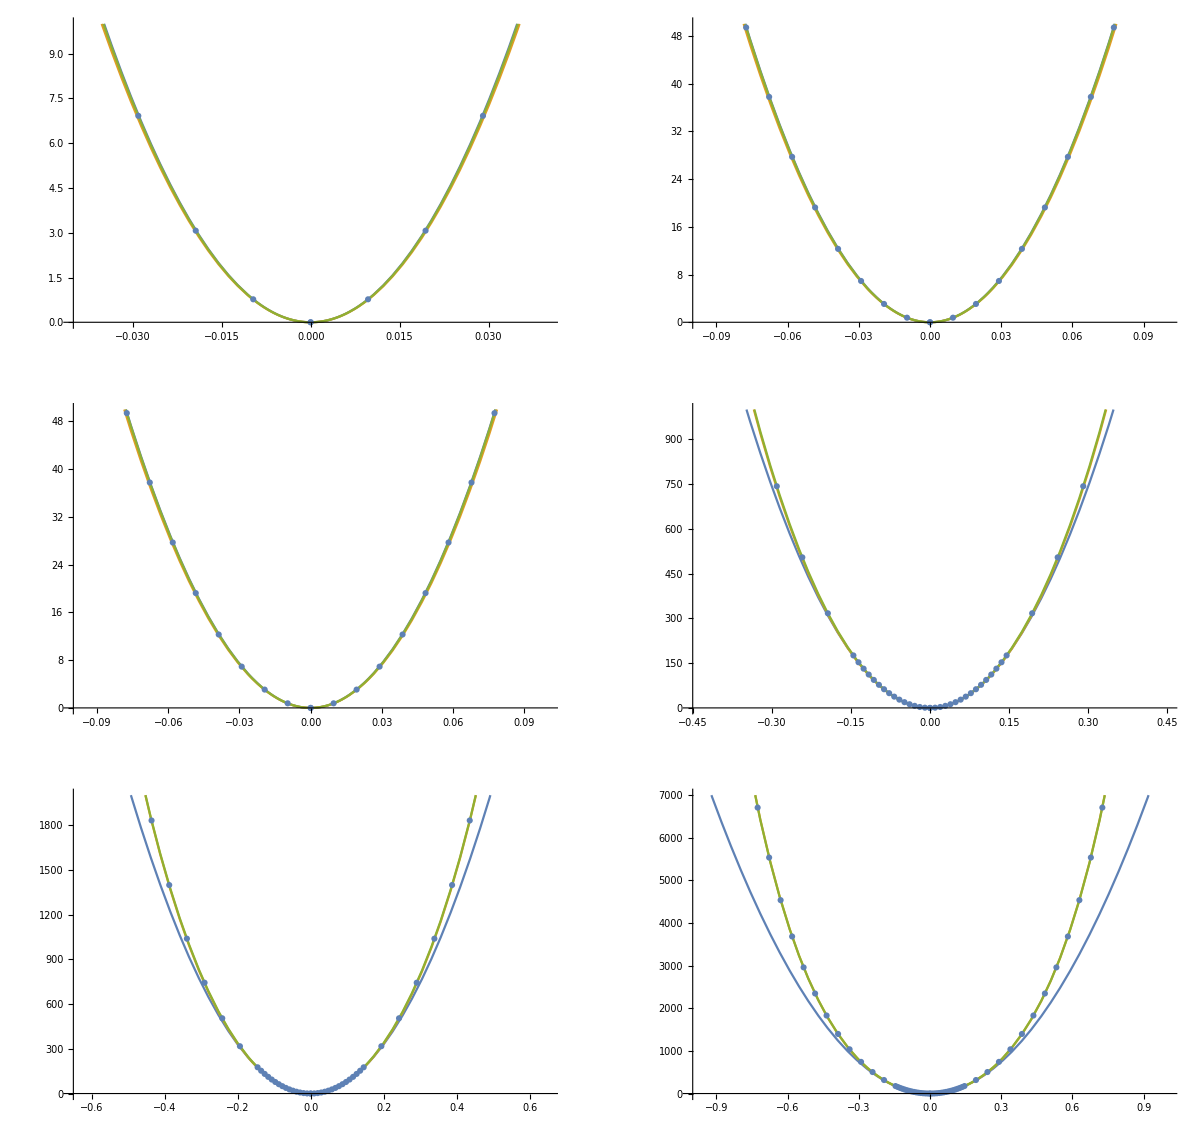

```mathematica
Look at fits at different scales - Zirconium;
P00z=With[{B=0.04,H=10},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,6,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P0z=With[{B=0.1,H=50},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,6,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P1z=With[{B=0.1,H=50},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,6,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P2z=With[{B=0.45,H=1000},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,6,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P3z=With[{B=0.65,H=2000},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,6,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P4z=With[{B=1,H=7000},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,6,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
GraphicsGrid[{{Show[P00z,ListPlot@zPlotData],Show[P0z,ListPlot@zPlotData]},{Show[P1z,ListPlot@zPlotData],Show[P2z,ListPlot@zPlotData]},{Show[P3z,ListPlot@zPlotData],Show[P4z,ListPlot@zPlotData]}},ImageSize->1200]
```

```mathematica
Carbon and zirconium - calculate harmonic frequency of fit (as root of prefactor *2 over mass);
(*If the fitted carbon potential is f(x)=A*x*x, let it be equal to standard harmonic expression, f(x)=A*x*x=1/2*m*omega*omega*x*x*)
"Carbon harmonic polynomial fit prefactor 'A' in meV/Ang**2 is"
Acarbon=V[1,2,x][[1]]
"cOmega0 in meV/Ang**2/AMU is approximately"
cOmega0=Sqrt[2Acarbon/m[[1]]]
"Zr harmonic polynomial fit prefactor 'A' in meV/Ang**2 is"
Azirconium=V[2,2,x][[1]]
"Z_Omega_0 in meV/Ang**2/AMU is approximately"
zOmega0=Sqrt[2Azirconium/m[[2]]]
```

Carbon harmonic polynomial fit prefactor 'A' in meV/Ang**2 is

5991.98

cOmega0 in meV/Ang**2/AMU is approximately

31.5875

Zr harmonic polynomial fit prefactor 'A' in meV/Ang**2 is

8248.72

Z_Omega_0 in meV/Ang**2/AMU is approximately

13.4479

```mathematica
Carbon and zirconium - calculate eigenvalues and vectors;
(*Find the first 70 eigenvalues and eigenvectors*)
Neigenvalues=70;
(*Define bounds for plotting and solving eigenproblem*)
B=1;H=2000;
(*Carbon Hamiltonians - from harmonic, even symmetry to 12th order*)
ℒall=Table[-(1/(2m[[1]]))*u''[x]+V[1,i,x]*u[x],{i,2,12,2}];
(*Zirconium Hamiltonians - harmonic, even symmetry to 12th order*)
ℒallz=Table[-(1/(2m[[2]]))*u''[x]+V[2,i,x]*u[x],{i,2,12,2}];
(*Carbon eigensystem*)
eigensysC=Table[NDEigensystem[ℒall[[j]],u[x],{x,-B,B},Neigenvalues,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}],{j,1,6}];
(*Zironcium eigensystem*)
eigensysZ=Table[NDEigensystem[ℒallz[[j]],u[x],{x,-B,B},Neigenvalues,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}],{j,1,6}];
```

```mathematica
(*Carbon and Zironcium eigenenergies*)
(*Indexed like 1 is harmonic, 2 is 4th order ... 6 is 12th order*)
eigenEnergies=Table[eigensysC[[k]][[1]]/cOmega0,{k,1,6}];
eigenEnergiesZ=Table[eigensysZ[[k]][[1]]/zOmega0,{k,1,6}];
```

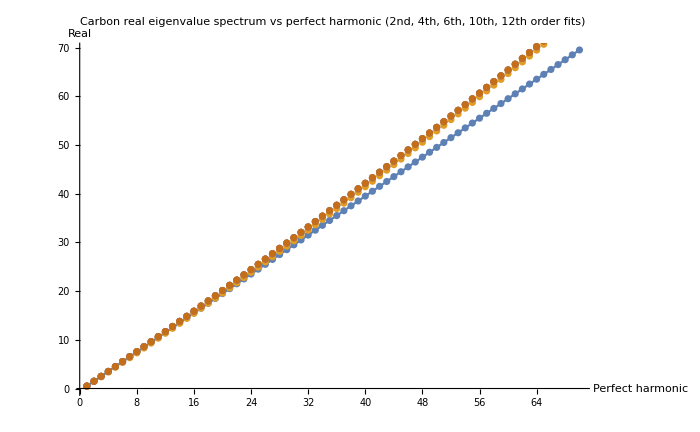

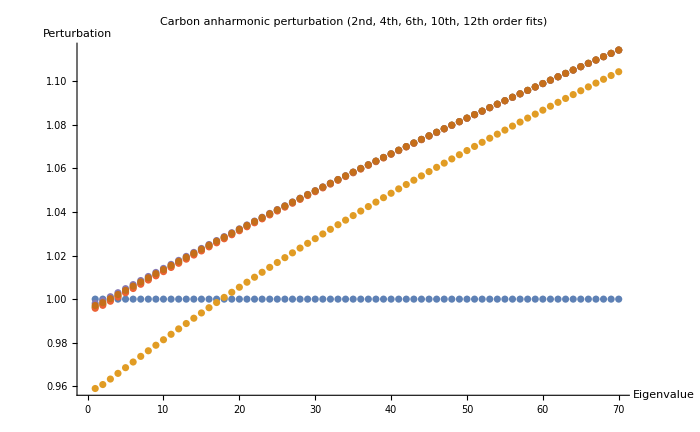

0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5 | 15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5 | 30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5 | 40.5 | 41.5 | 42.5 | 43.5 | 44.5 | 45.5 | 46.5 | 47.5 | 48.5 | 49.5 | 50.5 | 51.5 | 52.5 | 53.5 | 54.5 | 55.5 | 56.5 | 57.5 | 58.5 | 59.5 | 60.5 | 61.5 | 62.5 | 63.5 | 64.5 | 65.5 | 66.5 | 67.5 | 68.5 | 69.5
0.479489 | 1.44119 | 2.40831 | 3.38075 | 4.35843 | 5.34129 | 6.32924 | 7.32221 | 8.32013 | 9.32294 | 10.3306 | 11.343 | 12.36 | 13.3818 | 14.4081 | 15.4389 | 16.4742 | 17.514 | 18.5581 | 19.6065 | 20.6593 | 21.7162 | 22.7773 | 23.8426 | 24.912 | 25.9855 | 27.0629 | 28.1444 | 29.2298 | 30.3191 | 31.4123 | 32.5093 | 33.6101 | 34.7147 | 35.823 | 36.935 | 38.0506 | 39.17 | 40.2929 | 41.4194 | 42.5494 | 43.683 | 44.8201 | 45.9606 | 47.1046 | 48.252 | 49.4028 | 50.5569 | 51.7144 | 52.8752 | 54.0392 | 55.2066 | 56.3772 | 57.551 | 58.728 | 59.9082 | 61.0915 | 62.278 | 63.4676 | 64.6603 | 65.856 | 67.0548 | 68.2567 | 69.4615 | 70.6694 | 71.8802 | 73.094 | 74.3108 | 75.5305 | 76.753
0.498191 | 1.49657 | 2.49893 | 3.50523 | 4.51544 | 5.52954 | 6.54748 | 7.56925 | 8.5948 | 9.62412 | 10.6572 | 11.6939 | 12.7344 | 13.7785 | 14.8262 | 15.8775 | 16.9324 | 17.9909 | 19.0528 | 20.1183 | 21.1873 | 22.2597 | 23.3356 | 24.4149 | 25.4976 | 26.5836 | 27.673 | 28.7658 | 29.8618 | 30.9612 | 32.0638 | 33.1697 | 34.2789 | 35.3912 | 36.5068 | 37.6255 | 38.7474 | 39.8725 | 41.0006 | 42.132 | 43.2664 | 44.4039 | 45.5444 | 46.688 | 47.8347 | 48.9844 | 50.137 | 51.2927 | 52.4514 | 53.613 | 54.7776 | 55.9451 | 57.1155 | 58.2889 | 59.4651 | 60.6442 | 61.8262 | 63.0111 | 64.1988 | 65.3893 | 66.5826 | 67.7788 | 68.9778 | 70.1795 | 71.384 | 72.5913 | 73.8013 | 75.0141 | 76.2295 | 77.4477
0.497904 | 1.49573 | 2.49756 | 3.50337 | 4.51313 | 5.52679 | 6.54434 | 7.56573 | 8.59094 | 9.61994 | 10.6527 | 11.6892 | 12.7294 | 13.7732 | 14.8207 | 15.8719 | 16.9266 | 17.9849 | 19.0467 | 20.1121 | 21.181 | 22.2533 | 23.3291 | 24.4083 | 25.491 | 26.577 | 27.6664 | 28.7591 | 29.8551 | 30.9545 | 32.0572 | 33.1631 | 34.2722 | 35.3846 | 36.5002 | 37.619 | 38.7409 | 39.8661 | 40.9943 | 42.1257 | 43.2602 | 44.3978 | 45.5384 | 46.6821 | 47.8289 | 48.9787 | 50.1314 | 51.2872 | 52.446 | 53.6077 | 54.7724 | 55.94 | 57.1106 | 58.2841 | 59.4604 | 60.6397 | 61.8218 | 63.0068 | 64.1946 | 65.3852 | 66.5787 | 67.775 | 68.9741 | 70.176 | 71.3806 | 72.588 | 73.7981 | 75.011 | 76.2266 | 77.445
0.499024 | 1.49898 | 2.50275 | 3.5103 | 4.52162 | 5.53668 | 6.55546 | 7.57794 | 8.60411 | 9.63393 | 10.6674 | 11.7045 | 12.7451 | 13.7894 | 14.8372 | 15.8886 | 16.9434 | 18.0018 | 19.0636 | 20.129 | 21.1977 | 22.2699 | 23.3455 | 24.4244 | 25.5068 | 26.5925 | 27.6815 | 28.7739 | 29.8695 | 30.9684 | 32.0706 | 33.1761 | 34.2847 | 35.3966 | 36.5117 | 37.63 | 38.7514 | 39.876 | 41.0037 | 42.1346 | 43.2686 | 44.4056 | 45.5457 | 46.6889 | 47.8352 | 48.9844 | 50.1367 | 51.292 | 52.4503 | 53.6116 | 54.7758 | 55.943 | 57.1131 | 58.2861 | 59.4621 | 60.6409 | 61.8227 | 63.0073 | 64.1947 | 65.385 | 66.5782 | 67.7741 | 68.9729 | 70.1745 | 71.3789 | 72.586 | 73.7959 | 75.0086 | 76.224 | 77.4421
0.498536 | 1.49758 | 2.50057 | 3.50745 | 4.51821 | 5.53281 | 6.55121 | 7.5734 | 8.59933 | 9.62899 | 10.6624 | 11.6994 | 12.7401 | 13.7843 | 14.8322 | 15.8837 | 16.9387 | 17.9972 | 19.0592 | 20.1248 | 21.1937 | 22.2661 | 23.3419 | 24.4211 | 25.5037 | 26.5897 | 27.679 | 28.7715 | 29.8674 | 30.9666 | 32.069 | 33.1747 | 34.2836 | 35.3957 | 36.5111 | 37.6295 | 38.7512 | 39.876 | 41.0039 | 42.1349 | 43.269 | 44.4062 | 45.5465 | 46.6898 | 47.8362 | 48.9856 | 50.138 | 51.2933 | 52.4517 | 53.613 | 54.7773 | 55.9446 | 57.1147 | 58.2878 | 59.4638 | 60.6426 | 61.8244 | 63.009 | 64.1964 | 65.3867 | 66.5798 | 67.7758 | 68.9745 | 70.176 | 71.3803 | 72.5874 | 73.7973 | 75.0099 | 76.2252 | 77.4432

1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.958978 | 0.960795 | 0.963323 | 0.965928 | 0.968541 | 0.971143 | 0.973729 | 0.976294 | 0.978839 | 0.981362 | 0.983864 | 0.986344 | 0.988803 | 0.991242 | 0.993661 | 0.99606 | 0.998439 | 1.0008 | 1.00314 | 1.00546 | 1.00777 | 1.01006 | 1.01233 | 1.01458 | 1.01682 | 1.01904 | 1.02124 | 1.02343 | 1.02561 | 1.02777 | 1.02991 | 1.03204 | 1.03416 | 1.03626 | 1.03835 | 1.04042 | 1.04248 | 1.04453 | 1.04657 | 1.04859 | 1.0506 | 1.0526 | 1.05459 | 1.05657 | 1.05853 | 1.06048 | 1.06242 | 1.06436 | 1.06628 | 1.06818 | 1.07008 | 1.07197 | 1.07385 | 1.07572 | 1.07758 | 1.07943 | 1.08127 | 1.0831 | 1.08492 | 1.08673 | 1.08853 | 1.09032 | 1.09211 | 1.09388 | 1.09565 | 1.09741 | 1.09916 | 1.1009 | 1.10263 | 1.10436
0.996383 | 0.997714 | 0.999571 | 1.00149 | 1.00343 | 1.00537 | 1.0073 | 1.00923 | 1.01115 | 1.01307 | 1.01497 | 1.01686 | 1.01875 | 1.02063 | 1.0225 | 1.02435 | 1.02621 | 1.02805 | 1.02988 | 1.03171 | 1.03353 | 1.03534 | 1.03714 | 1.03893 | 1.04072 | 1.0425 | 1.04427 | 1.04603 | 1.04778 | 1.04953 | 1.05127 | 1.05301 | 1.05473 | 1.05645 | 1.05817 | 1.05987 | 1.06157 | 1.06327 | 1.06495 | 1.06663 | 1.06831 | 1.06997 | 1.07163 | 1.07329 | 1.07494 | 1.07658 | 1.07822 | 1.07985 | 1.08147 | 1.08309 | 1.0847 | 1.08631 | 1.08791 | 1.08951 | 1.0911 | 1.09269 | 1.09427 | 1.09584 | 1.09741 | 1.09898 | 1.10054 | 1.10209 | 1.10364 | 1.10519 | 1.10673 | 1.10826 | 1.10979 | 1.11132 | 1.11284 | 1.11436
0.995807 | 0.99715 | 0.999024 | 1.00096 | 1.00292 | 1.00487 | 1.00682 | 1.00876 | 1.0107 | 1.01263 | 1.01454 | 1.01645 | 1.01835 | 1.02024 | 1.02212 | 1.02399 | 1.02585 | 1.02771 | 1.02955 | 1.03139 | 1.03322 | 1.03504 | 1.03685 | 1.03865 | 1.04045 | 1.04223 | 1.04401 | 1.04579 | 1.04755 | 1.04931 | 1.05105 | 1.0528 | 1.05453 | 1.05626 | 1.05798 | 1.05969 | 1.0614 | 1.0631 | 1.06479 | 1.06647 | 1.06815 | 1.06983 | 1.07149 | 1.07315 | 1.07481 | 1.07645 | 1.0781 | 1.07973 | 1.08136 | 1.08298 | 1.0846 | 1.08621 | 1.08782 | 1.08942 | 1.09102 | 1.09261 | 1.09419 | 1.09577 | 1.09734 | 1.09891 | 1.10047 | 1.10203 | 1.10359 | 1.10513 | 1.10668 | 1.10821 | 1.10975 | 1.11127 | 1.1128 | 1.11432
0.998048 | 0.999321 | 1.0011 | 1.00294 | 1.0048 | 1.00667 | 1.00853 | 1.01039 | 1.01225 | 1.0141 | 1.01594 | 1.01778 | 1.01961 | 1.02144 | 1.02326 | 1.02507 | 1.02687 | 1.02867 | 1.03047 | 1.03225 | 1.03403 | 1.03581 | 1.03758 | 1.03934 | 1.04109 | 1.04284 | 1.04459 | 1.04632 | 1.04805 | 1.04978 | 1.0515 | 1.05321 | 1.05491 | 1.05662 | 1.05831 | 1.06 | 1.06168 | 1.06336 | 1.06503 | 1.0667 | 1.06836 | 1.07001 | 1.07166 | 1.07331 | 1.07495 | 1.07658 | 1.07821 | 1.07983 | 1.08145 | 1.08306 | 1.08467 | 1.08627 | 1.08787 | 1.08946 | 1.09105 | 1.09263 | 1.09421 | 1.09578 | 1.09735 | 1.09891 | 1.10047 | 1.10202 | 1.10357 | 1.10511 | 1.10665 | 1.10818 | 1.10971 | 1.11124 | 1.11276 | 1.11427
0.997073 | 0.99839 | 1.00023 | 1.00213 | 1.00405 | 1.00596 | 1.00788 | 1.00979 | 1.01169 | 1.01358 | 1.01546 | 1.01734 | 1.0192 | 1.02106 | 1.02291 | 1.02475 | 1.02659 | 1.02841 | 1.03023 | 1.03204 | 1.03384 | 1.03563 | 1.03742 | 1.0392 | 1.04097 | 1.04273 | 1.04449 | 1.04624 | 1.04798 | 1.04972 | 1.05144 | 1.05317 | 1.05488 | 1.05659 | 1.05829 | 1.05999 | 1.06168 | 1.06336 | 1.06504 | 1.06671 | 1.06837 | 1.07003 | 1.07168 | 1.07333 | 1.07497 | 1.07661 | 1.07824 | 1.07986 | 1.08148 | 1.08309 | 1.0847 | 1.0863 | 1.0879 | 1.08949 | 1.09108 | 1.09266 | 1.09424 | 1.09581 | 1.09737 | 1.09894 | 1.10049 | 1.10204 | 1.10359 | 1.10513 | 1.10667 | 1.1082 | 1.10973 | 1.11126 | 1.11278 | 1.11429

```mathematica
Carbon - look at harmonic and anharmonic eigenvalues;
(*Omega=31.58754341976066;M=12;V[x_,M_,Omega_]:=0.5*Omega*Omega*M*x^2*)
cOmega0=31.58754341976066;
eigenEnergies=Table[eigensysC[[k]][[1]]/cOmega0,{k,1,6}];
Show[Plot[f[x]=x-0.5,{x,1,Neigenvalues},PlotLabel->"Carbon real eigenvalue spectrum vs perfect harmonic \n(2nd, 4th, 6th, 10th, 12th order fits)",AxesLabel->{"Perfect harmonic","Real"}],ListPlot@eigenEnergies,ImageSize->700]
Show[ListPlot[relativeEigenval,PlotLabel->"Carbon anharmonic perturbation \n(2nd, 4th, 6th, 10th, 12th order fits)",AxesLabel->{"Eigenvalue","Perturbation"}],ImageSize->700]
relativeEigenval=Table[eigensysC[[k]][[1]]/eigensysC[[1]][[1]],{k,1,6}];
eigenEnergies//TableForm
relativeEigenval//TableForm
```

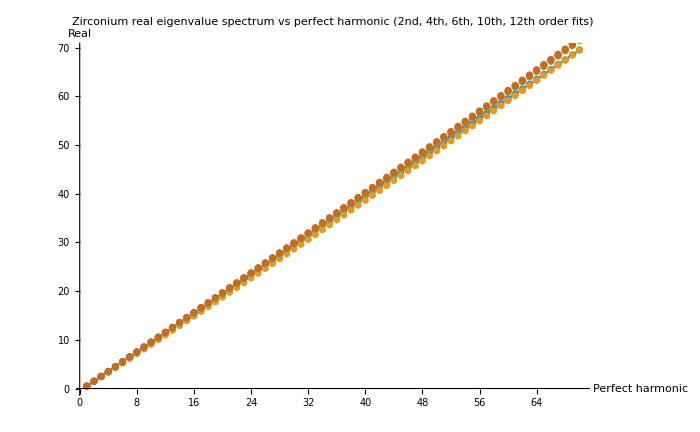

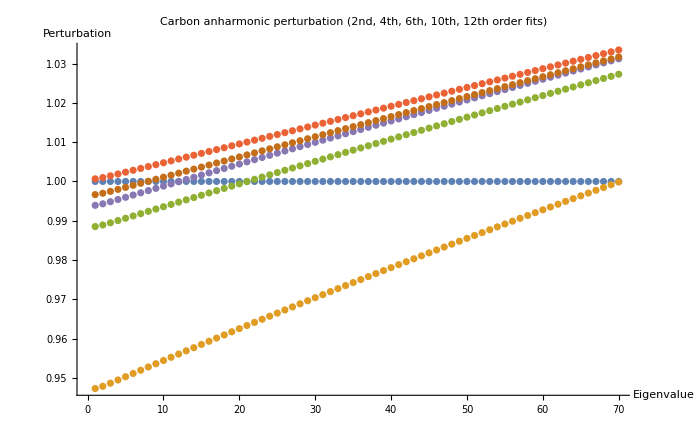

0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5 | 15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5 | 30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5 | 40.5 | 41.5 | 42.5 | 43.5 | 44.5 | 45.5 | 46.5 | 47.5 | 48.5 | 49.5 | 50.5 | 51.5 | 52.5 | 53.5 | 54.5 | 55.5 | 56.5 | 57.5 | 58.5 | 59.5 | 60.5 | 61.5 | 62.5 | 63.5 | 64.5 | 65.5 | 66.5 | 67.5001 | 68.5001 | 69.5001
0.47367 | 1.42185 | 2.37173 | 3.32328 | 4.2765 | 5.23139 | 6.18793 | 7.14612 | 8.10595 | 9.0674 | 10.0305 | 10.9952 | 11.9615 | 12.9294 | 13.8989 | 14.87 | 15.8426 | 16.8169 | 17.7927 | 18.77 | 19.7489 | 20.7294 | 21.7114 | 22.6949 | 23.68 | 24.6665 | 25.6546 | 26.6442 | 27.6352 | 28.6278 | 29.6219 | 30.6174 | 31.6144 | 32.6129 | 33.6129 | 34.6143 | 35.6171 | 36.6214 | 37.6271 | 38.6343 | 39.6429 | 40.6529 | 41.6644 | 42.6772 | 43.6915 | 44.7071 | 45.7242 | 46.7426 | 47.7625 | 48.7837 | 49.8063 | 50.8303 | 51.8556 | 52.8823 | 53.9103 | 54.9397 | 55.9705 | 57.0025 | 58.036 | 59.0707 | 60.1068 | 61.1442 | 62.183 | 63.223 | 64.2644 | 65.307 | 66.351 | 67.3962 | 68.4428 | 69.4906
0.494269 | 1.4834 | 2.47372 | 3.46522 | 4.4579 | 5.45176 | 6.4468 | 7.44301 | 8.44039 | 9.43893 | 10.4386 | 11.4395 | 12.4416 | 13.4447 | 14.4491 | 15.4546 | 16.4612 | 17.469 | 18.478 | 19.488 | 20.4992 | 21.5116 | 22.5251 | 23.5397 | 24.5554 | 25.5723 | 26.5903 | 27.6094 | 28.6297 | 29.651 | 30.6735 | 31.6971 | 32.7218 | 33.7476 | 34.7745 | 35.8025 | 36.8316 | 37.8618 | 38.8931 | 39.9255 | 40.959 | 41.9936 | 43.0293 | 44.066 | 45.1039 | 46.1428 | 47.1828 | 48.2239 | 49.266 | 50.3093 | 51.3535 | 52.3989 | 53.4453 | 54.4928 | 55.5414 | 56.591 | 57.6417 | 58.6934 | 59.7462 | 60.8 | 61.8549 | 62.9109 | 63.9679 | 65.0259 | 66.085 | 67.1451 | 68.2062 | 69.2684 | 70.3316 | 71.3959
0.500333 | 1.50148 | 2.50358 | 3.50664 | 4.51067 | 5.51565 | 6.52159 | 7.52849 | 8.53635 | 9.54517 | 10.5549 | 11.5657 | 12.5774 | 13.59 | 14.6036 | 15.6182 | 16.6338 | 17.6503 | 18.6677 | 19.6861 | 20.7055 | 21.7258 | 22.7471 | 23.7694 | 24.7926 | 25.8167 | 26.8418 | 27.8679 | 28.895 | 29.923 | 30.9519 | 31.9818 | 33.0127 | 34.0445 | 35.0773 | 36.111 | 37.1457 | 38.1814 | 39.218 | 40.2555 | 41.294 | 42.3335 | 43.3739 | 44.4153 | 45.4576 | 46.5009 | 47.5451 | 48.5903 | 49.6365 | 50.6835 | 51.7316 | 52.7806 | 53.8305 | 54.8814 | 55.9332 | 56.986 | 58.0398 | 59.0945 | 60.1501 | 61.2067 | 62.2642 | 63.3227 | 64.3821 | 65.4425 | 66.5038 | 67.566 | 68.6292 | 69.6934 | 70.7584 | 71.8245
0.496964 | 1.49147 | 2.48712 | 3.48393 | 4.48188 | 5.48097 | 6.4812 | 7.48257 | 8.48507 | 9.4887 | 10.4934 | 11.4993 | 12.5063 | 13.5144 | 14.5237 | 15.534 | 16.5454 | 17.558 | 18.5716 | 19.5864 | 20.6022 | 21.6191 | 22.6372 | 23.6563 | 24.6765 | 25.6977 | 26.7201 | 27.7435 | 28.768 | 29.7936 | 30.8203 | 31.848 | 32.8767 | 33.9066 | 34.9375 | 35.9694 | 37.0024 | 38.0365 | 39.0716 | 40.1077 | 41.1449 | 42.1832 | 43.2225 | 44.2628 | 45.3041 | 46.3465 | 47.3899 | 48.4344 | 49.4798 | 50.5263 | 51.5739 | 52.6224 | 53.6719 | 54.7225 | 55.7741 | 56.8267 | 57.8803 | 58.9349 | 59.9906 | 61.0472 | 62.1048 | 63.1635 | 64.2231 | 65.2837 | 66.3454 | 67.408 | 68.4716 | 69.5362 | 70.6018 | 71.6684
0.498328 | 1.4955 | 2.49371 | 3.49296 | 4.49325 | 5.49458 | 6.49694 | 7.50033 | 8.50477 | 9.51023 | 10.5167 | 11.5243 | 12.5328 | 13.5424 | 14.5531 | 15.5647 | 16.5774 | 17.5911 | 18.6059 | 19.6217 | 20.6385 | 21.6563 | 22.6751 | 23.695 | 24.7159 | 25.7378 | 26.7608 | 27.7848 | 28.8097 | 29.8357 | 30.8628 | 31.8908 | 32.9199 | 33.9499 | 34.981 | 36.0131 | 37.0463 | 38.0804 | 39.1155 | 40.1517 | 41.1888 | 42.227 | 43.2662 | 44.3063 | 45.3475 | 46.3897 | 47.4329 | 48.4771 | 49.5223 | 50.5685 | 51.6157 | 52.6638 | 53.713 | 54.7632 | 55.8144 | 56.8665 | 57.9197 | 58.9739 | 60.029 | 61.0851 | 62.1422 | 63.2003 | 64.2594 | 65.3195 | 66.3806 | 67.4426 | 68.5056 | 69.5696 | 70.6346 | 71.7006

1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.947339 | 0.947903 | 0.948691 | 0.949509 | 0.950334 | 0.951162 | 0.951989 | 0.952816 | 0.953641 | 0.954464 | 0.955284 | 0.956103 | 0.956919 | 0.957733 | 0.958544 | 0.959353 | 0.96016 | 0.960964 | 0.961766 | 0.962566 | 0.963363 | 0.964158 | 0.96495 | 0.965741 | 0.966529 | 0.967314 | 0.968098 | 0.968879 | 0.969658 | 0.970434 | 0.971209 | 0.971981 | 0.972752 | 0.97352 | 0.974285 | 0.975049 | 0.975811 | 0.976571 | 0.977328 | 0.978084 | 0.978837 | 0.979588 | 0.980338 | 0.981085 | 0.981831 | 0.982574 | 0.983316 | 0.984055 | 0.984793 | 0.985529 | 0.986263 | 0.986995 | 0.987725 | 0.988453 | 0.98918 | 0.989904 | 0.990627 | 0.991348 | 0.992067 | 0.992785 | 0.9935 | 0.994214 | 0.994927 | 0.995637 | 0.996346 | 0.997053 | 0.997758 | 0.998462 | 0.999164 | 0.999864
0.988537 | 0.988933 | 0.989487 | 0.990063 | 0.990645 | 0.99123 | 0.991815 | 0.992401 | 0.992987 | 0.993572 | 0.994157 | 0.994741 | 0.995324 | 0.995907 | 0.996489 | 0.99707 | 0.99765 | 0.99823 | 0.998808 | 0.999386 | 0.999963 | 1.00054 | 1.00111 | 1.00169 | 1.00226 | 1.00284 | 1.00341 | 1.00398 | 1.00455 | 1.00512 | 1.00569 | 1.00626 | 1.00682 | 1.00739 | 1.00796 | 1.00852 | 1.00909 | 1.00965 | 1.01021 | 1.01077 | 1.01133 | 1.01189 | 1.01245 | 1.01301 | 1.01357 | 1.01413 | 1.01468 | 1.01524 | 1.01579 | 1.01635 | 1.0169 | 1.01745 | 1.01801 | 1.01856 | 1.01911 | 1.01966 | 1.02021 | 1.02075 | 1.0213 | 1.02185 | 1.0224 | 1.02294 | 1.02349 | 1.02403 | 1.02457 | 1.02511 | 1.02566 | 1.0262 | 1.02674 | 1.02728
1.00067 | 1.00099 | 1.00143 | 1.0019 | 1.00237 | 1.00285 | 1.00332 | 1.0038 | 1.00428 | 1.00475 | 1.00523 | 1.00571 | 1.00619 | 1.00667 | 1.00715 | 1.00763 | 1.00811 | 1.00859 | 1.00906 | 1.00954 | 1.01002 | 1.0105 | 1.01098 | 1.01146 | 1.01194 | 1.01242 | 1.0129 | 1.01338 | 1.01386 | 1.01434 | 1.01482 | 1.0153 | 1.01577 | 1.01625 | 1.01673 | 1.01721 | 1.01769 | 1.01817 | 1.01865 | 1.01913 | 1.01961 | 1.02008 | 1.02056 | 1.02104 | 1.02152 | 1.022 | 1.02248 | 1.02295 | 1.02343 | 1.02391 | 1.02439 | 1.02487 | 1.02534 | 1.02582 | 1.0263 | 1.02677 | 1.02725 | 1.02773 | 1.02821 | 1.02868 | 1.02916 | 1.02964 | 1.03011 | 1.03059 | 1.03107 | 1.03154 | 1.03202 | 1.03249 | 1.03297 | 1.03344
0.993927 | 0.994312 | 0.99485 | 0.995409 | 0.995973 | 0.996541 | 0.997108 | 0.997676 | 0.998243 | 0.99881 | 0.999376 | 0.999941 | 1.00051 | 1.00107 | 1.00163 | 1.00219 | 1.00275 | 1.00331 | 1.00387 | 1.00443 | 1.00499 | 1.00554 | 1.0061 | 1.00665 | 1.0072 | 1.00775 | 1.00831 | 1.00886 | 1.0094 | 1.00995 | 1.0105 | 1.01105 | 1.01159 | 1.01214 | 1.01268 | 1.01322 | 1.01376 | 1.01431 | 1.01485 | 1.01539 | 1.01592 | 1.01646 | 1.017 | 1.01753 | 1.01807 | 1.0186 | 1.01914 | 1.01967 | 1.0202 | 1.02073 | 1.02126 | 1.02179 | 1.02232 | 1.02285 | 1.02338 | 1.0239 | 1.02443 | 1.02496 | 1.02548 | 1.026 | 1.02653 | 1.02705 | 1.02757 | 1.02809 | 1.02861 | 1.02913 | 1.02965 | 1.03017 | 1.03068 | 1.0312
0.996655 | 0.997001 | 0.997486 | 0.99799 | 0.998501 | 0.999014 | 0.999529 | 1.00004 | 1.00056 | 1.00108 | 1.00159 | 1.00211 | 1.00263 | 1.00314 | 1.00366 | 1.00418 | 1.00469 | 1.00521 | 1.00572 | 1.00624 | 1.00675 | 1.00727 | 1.00778 | 1.0083 | 1.00881 | 1.00933 | 1.00984 | 1.01035 | 1.01087 | 1.01138 | 1.01189 | 1.01241 | 1.01292 | 1.01343 | 1.01394 | 1.01445 | 1.01497 | 1.01548 | 1.01599 | 1.0165 | 1.01701 | 1.01752 | 1.01803 | 1.01854 | 1.01905 | 1.01955 | 1.02006 | 1.02057 | 1.02108 | 1.02158 | 1.02209 | 1.0226 | 1.0231 | 1.02361 | 1.02412 | 1.02462 | 1.02513 | 1.02563 | 1.02614 | 1.02664 | 1.02714 | 1.02765 | 1.02815 | 1.02865 | 1.02916 | 1.02966 | 1.03016 | 1.03066 | 1.03116 | 1.03166

```mathematica
Zirconium - look at harmonic and anharmonic eigenvalues;
(*zOmega=13.44788050977517;M=91;V[x_,M_,Omega_]:=0.5*Omega*Omega*M*x^2*)
zOmega0=13.44788050977517;
eigenEnergiesZ=Table[eigensysZ[[k]][[1]]/zOmega0,{k,1,6}];
Show[Plot[f[x]=x-0.5,{x,1,Neigenvalues},PlotLabel->"Zirconium real eigenvalue spectrum vs perfect harmonic \n(2nd, 4th, 6th, 10th, 12th order fits)",AxesLabel->{"Perfect harmonic","Real"}],ListPlot@eigenEnergiesZ,ImageSize->700]
relativeEigenvalz=Table[eigensysZ[[k]][[1]]/eigensysZ[[1]][[1]],{k,1,6}];
Show[ListPlot[relativeEigenvalz,ImageSize->700,PlotLabel->"Carbon anharmonic perturbation \n(2nd, 4th, 6th, 10th, 12th order fits)",AxesLabel->{"Eigenvalue","Perturbation"}]]
eigenEnergiesZ//TableForm
relativeEigenvalz//TableForm
```

{1.,1.10436,1.11436,1.11432,1.11427,1.11429}

{1.,0.999864,1.02728,1.03344,1.0312,1.03166}

{ImageSize→600,PlotLegends→SwatchLegend[{10th eigenvalue,20th eigenvalue,30th eigenvalue,40th eigenvalue,50th eigenvalue,60th eigenvalue,70th eigenvalue}],PlotLabel→Convergence of anharmonic perturbation with fit order,AxesLabel→{1/2 * Fit Order 
(2nd, 4th, 6th, 8th, 10th, 12th),Anharmonic
perturbation}}

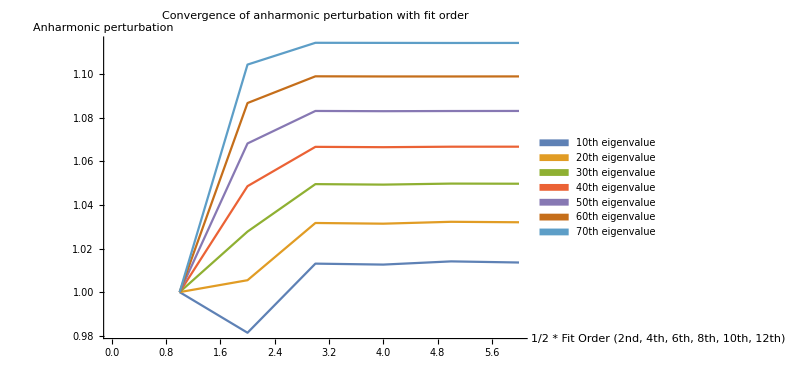

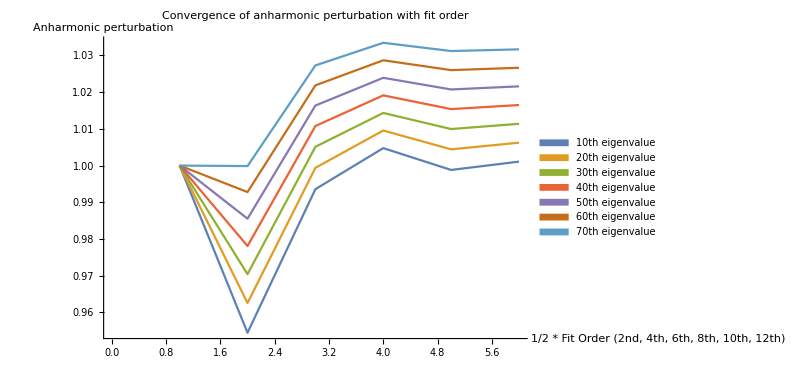

```mathematica
Carbon and zirconium - check convergence of eigenvalues with fit order;
Transpose[relativeEigenval][[70]]
Transpose[relativeEigenvalz][[70]]
plotstuff={ImageSize->600,PlotLegends->SwatchLegend[{"10th eigenvalue","20th eigenvalue","30th eigenvalue","40th eigenvalue","50th eigenvalue","60th eigenvalue","70th eigenvalue"}],PlotLabel->"Convergence of anharmonic perturbation with fit order",AxesLabel->{"1/2 * Fit Order \n(2nd, 4th, 6th, 8th, 10th, 12th)","Anharmonic\nperturbation"}}
ListPlot[Table[Transpose[relativeEigenval][[i]],{i,10,70,10}], Joined->True,plotstuff]
ListPlot[Table[Transpose[relativeEigenvalz][[i]],{i,10,70,10}], Joined->True,plotstuff]
```

```mathematica
Plot input stuff for Carbon eigensystem;
eigenPlots=Table[Show[Plot[Evaluate[(6*eigensysC[[i]][[2]])+eigensysC[[i]][[1]]],{x,-B,B}],Plot[Evaluate@V[1,2i,x],{x,-B,B}],PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}],{i,1,6}];
plotgrid={Table[eigenPlots[[i]],{i,1,2}],Table[eigenPlots[[j]],{j,3,4}],Table[eigenPlots[[k]],{k,5,6}]};
```

```mathematica
.
```

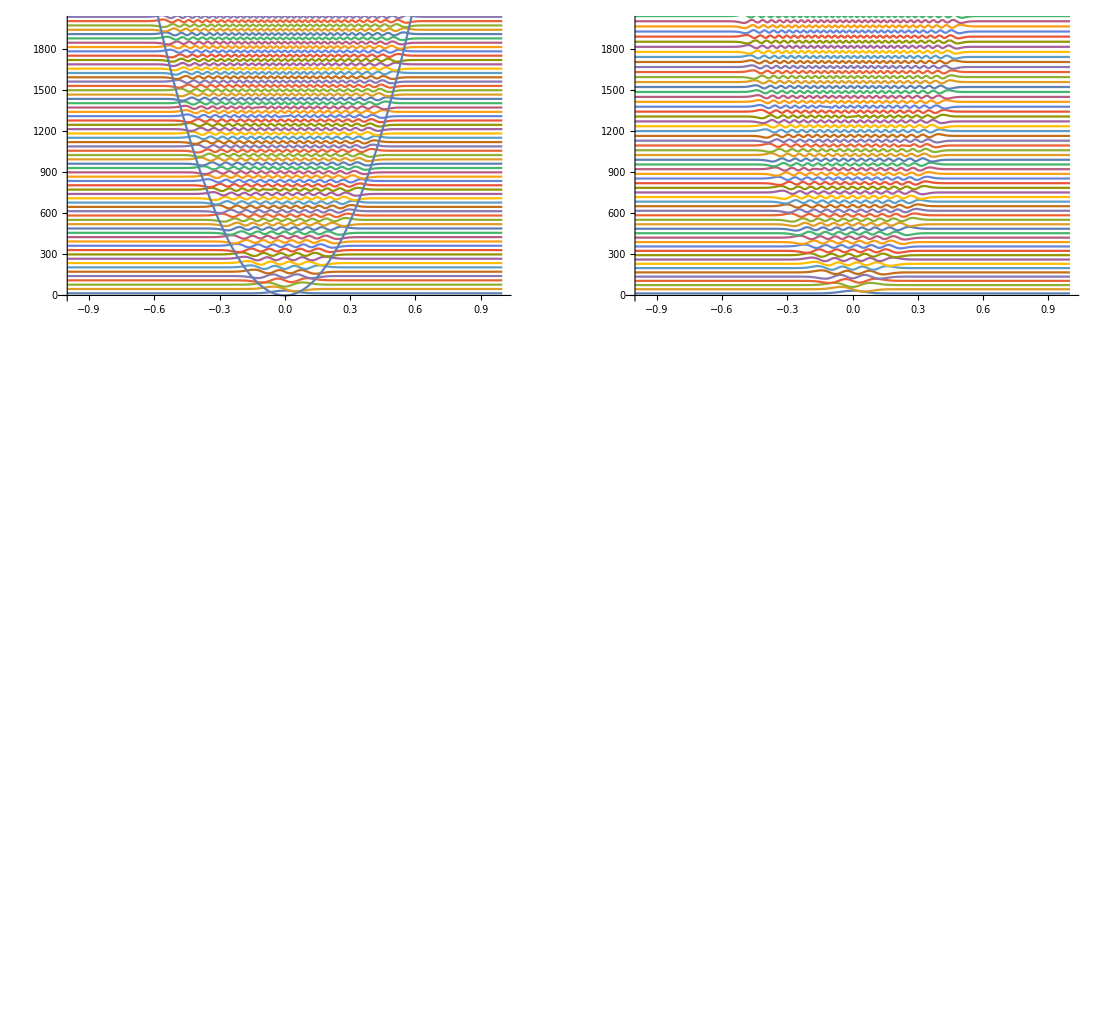

```mathematica
Plot carbon potential and eigensystem (eigenvectors and eigenvectors*eigenvalues);
GraphicsGrid[plotgrid,ImageSize->1100]
```

```mathematica
Plot input stuff for Zr eigensystem;
Bz=0.5;Hz=1000;
eigenPlotsz=Table[Show[Plot[Evaluate[(4*eigensysZ[[i]][[2]])+eigensysZ[[i]][[1]]],{x,-Bz,Bz}],Plot[Evaluate@V[2,2i,x],{x,-Bz,Bz}],PlotRange->{{-Bz,Bz},{0,Hz}},AxesOrigin->{-Bz,0}],{i,1,6}];
plotgrid={Table[eigenPlots[[i]],{i,1,2}],Table[eigenPlots[[j]],{j,3,4}],Table[eigenPlots[[k]],{k,5,6}]};
plotgridz={Table[eigenPlotsz[[i]],{i,1,2}],Table[eigenPlotsz[[j]],{j,3,4}],Table[eigenPlotsz[[k]],{k,5,6}]};
```

```mathematica
Plot zirconium eigensystem;
GraphicsGrid[plotgridz,ImageSize->1100]
```

-Graphics-

```mathematica
Carbon - fit an approximate analytic function to the anharmonic perturbation;
(*Make a function of different polynomial orders*)
anharmonicfit1=Fit[relativeEigenval[[5]],{1,x},x]
anharmonicfit2=Fit[relativeEigenval[[5]],{1, x, x^2},x]
anharmonicfit3=Fit[relativeEigenval[[5]],{1, x, x^2,x^3},x]
anharmonicfit4=Fit[relativeEigenval[[5]],{1, x, x^2,x^3,x^4},x]
Show[ListPlot[relativeEigenval[[5]],PlotLabel->"Carbon anharmonic pertubation vs eigenvalue \n and 1st, 2nd, 3rd, 4th order fits",AxesLabel->{"Eigenvalue","Anharmonic perturbation"}],Plot[{anharmonicfit1,anharmonicfit4},{x,1,70}],ImageSize->900]
```

0.997916+0.00169246 x

0.995552+0.00188943 x-2.77422×10^-6 x^2

0.995549+0.00189 x-2.79437×10^-6 x^2+1.8919×10^-10 x^3

0.995692+0.00185206 x-4.29005×10^-7 x^2-5.13864×10^-8 x^3+3.63208×10^-10 x^4

-Graphics-

```mathematica
Zirconium - fit an approximate analytic function to the anharmonic perturbation;
(*Make a function of different polynomial orders*)
anharmonicfit1z=Fit[relativeEigenvalz[[6]],{1,x},x]
anharmonicfit2z=Fit[relativeEigenvalz[[6]],{1, x, x^2},x]
anharmonicfit3z=Fit[relativeEigenvalz[[6]],{1, x, x^2,x^3},x]
anharmonicfit4z=Fit[relativeEigenvalz[[6]],{1, x, x^2,x^3,x^4},x]
Show[ListPlot[relativeEigenvalz[[6]],PlotLabel->"Zirconium anharmonic pertubation vs eigenvalue \n and 1st, 2nd, 3rd, 4th order fits",AxesLabel->{"Eigenvalue","Anharmonic perturbation"}],Plot[{anharmonicfit1z,anharmonicfit4z},{x,1,70}],ImageSize->900]
```

Null Zirconium

0.996021+0.000510629 x

0.995932+0.000518036 x-1.04332×10^-7 x^2

0.995977+0.000510718 x+1.51536×10^-7 x^2-2.40252×10^-9 x^3

0.996018+0.000499913 x+8.25116×10^-7 x^2-1.70896×10^-8 x^3+1.0343×10^-10 x^4

-Graphics-

```mathematica
(*Compare C and Zr anharmonic perturbations*)
Show[ListPlot[relativeEigenval[[5]],PlotLabel->"Zirconium and carbon anharmonic pertubation vs eigenvalue \n and 1st, 2nd, 3rd, 4th order fits",AxesLabel->{"Eigenvalue","Anharmonic perturbation"}],Plot[{anharmonicfit1,anharmonicfit4},{x,1,70}],ListPlot[relativeEigenvalz[[6]]],Plot[{anharmonicfit1z,anharmonicfit4z},{x,1,70}],ImageSize->900]
```

-Graphics-

```mathematica
Not finished - continue from here
```

-continue from here+finished Not

```mathematica
(*Plot derivitive of C and Zr anharmonic perturbation fits*)
cAnharmonicityDerivitive=D[{anharmonicfit1,anharmonicfit2,anharmonicfit3,anharmonicfit4},x]
zrAnharmonicityDerivitive=D[{anharmonicfit1z,anharmonicfit2z,anharmonicfit3z,anharmonicfit4z},x]
GraphicsGrid[{{Show@Plot[{cAnharmonicityDerivitive},{x,0,70},ImageSize->400],Show@Plot[{zrAnharmonicityDerivitive},{x,0,70}]}}]
```

{0.00169246,0.00188943-5.54844×10^-6 x,0.00189-5.58874×10^-6 x+5.67571×10^-10 x^2,0.00185206-8.58009×10^-7 x-1.54159×10^-7 x^2+1.45283×10^-9 x^3}

{0.000510629,0.000518036-2.08663×10^-7 x,0.000510718+3.03072×10^-7 x-7.20755×10^-9 x^2,0.000499913+1.65023×10^-6 x-5.12687×10^-8 x^2+4.1372×10^-10 x^3}

-Graphics-

```mathematica
(*Calculate partition function and Helmholtz free energy with Einstein frequencies*)
(*As previous, define omega0 as the solution to A*x*x=1/2*m*omega*omega*x*x, where A*x*x is the harmonic fit*)
"4.685Ang Einstein frequencies from polynomial fit:"
Acarbon=V[1,2,X][[1]];
cOmega0=Sqrt[2Acarbon/m[[1]]]
Azirconium=V[2,2,X][[1]];
zOmega0=Sqrt[2Azirconium/m[[2]]] 
(*Note, if we define the Einstein frequency in terms of the QHA DOS as the energy integrating up to which gives the number of modes equal to the 3*Natoms/2, then the frequencies are*)
"4.685Ang Einstein frequencies from QHA finding integration limit that gives 48 (3*Natoms/2) for each band:"
cOmegaInt48=65.1879672429008/2
zrOmegaInt48=26.329538754361874/2
"4.685Ang Einstein frequencies from QHA finding peak frequency for each band:"
cOmegaMaxPeak=4.14*18.0295229515/2
zrOmegaMaxPeak=4.14*6.2446881878/2
```

4.685Ang Einstein frequencies from polynomial fit:

31.5875

13.4479

4.685Ang Einstein frequencies from QHA finding integration limit that gives 48 (3*Natoms/2) for each band:

32.594

13.1648

4.685Ang Einstein frequencies from QHA finding peak frequency for each band:

37.3211

12.9265

```mathematica
(*Zirconium eigenspectrum*)
(*Ideal harmonic eigenvalue spectrum*)
perfectHarmonic=Table[0.5+i,{i,0,69}];
Partition[perfectHarmonic,15]//TableForm
(*2nd order fit harmonic eigenvalue spectrum*)
Partition[eigenEnergiesZ[[1]],15]//TableForm
(*12th order fit harmonic eigenvalue spectrum*)
Partition[eigenEnergiesZ[[6]],15]//TableForm
```

0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5
15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5
30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5 | 40.5 | 41.5 | 42.5 | 43.5 | 44.5
45.5 | 46.5 | 47.5 | 48.5 | 49.5 | 50.5 | 51.5 | 52.5 | 53.5 | 54.5 | 55.5 | 56.5 | 57.5 | 58.5 | 59.5

0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5
15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5
30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5 | 40.5 | 41.5 | 42.5 | 43.5 | 44.5
45.5 | 46.5 | 47.5 | 48.5 | 49.5 | 50.5 | 51.5 | 52.5 | 53.5 | 54.5 | 55.5 | 56.5 | 57.5 | 58.5 | 59.5

0.498328 | 1.4955 | 2.49371 | 3.49296 | 4.49325 | 5.49458 | 6.49694 | 7.50033 | 8.50477 | 9.51023 | 10.5167 | 11.5243 | 12.5328 | 13.5424 | 14.5531
15.5647 | 16.5774 | 17.5911 | 18.6059 | 19.6217 | 20.6385 | 21.6563 | 22.6751 | 23.695 | 24.7159 | 25.7378 | 26.7608 | 27.7848 | 28.8097 | 29.8357
30.8628 | 31.8908 | 32.9199 | 33.9499 | 34.981 | 36.0131 | 37.0463 | 38.0804 | 39.1155 | 40.1517 | 41.1888 | 42.227 | 43.2662 | 44.3063 | 45.3475
46.3897 | 47.4329 | 48.4771 | 49.5223 | 50.5685 | 51.6157 | 52.6638 | 53.713 | 54.7632 | 55.8144 | 56.8665 | 57.9197 | 58.9739 | 60.029 | 61.0851

```mathematica
(*Carbon eigenspectrum*)
(*Ideal harmonic eigenvalue spectrum*)
perfectHarmonic=Table[0.5+i,{i,0,69}];
Partition[perfectHarmonic,15]//TableForm
(*2nd order fit harmonic eigenvalue spectrum*)
Partition[eigenEnergies[[1]],15]//TableForm
(*12th order fit harmonic eigenvalue spectrum*)
Partition[eigenEnergies[[6]],15]//TableForm
```

0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5
15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5
30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5 | 40.5 | 41.5 | 42.5 | 43.5 | 44.5
45.5 | 46.5 | 47.5 | 48.5 | 49.5 | 50.5 | 51.5 | 52.5 | 53.5 | 54.5 | 55.5 | 56.5 | 57.5 | 58.5 | 59.5

0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5
15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5
30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5 | 40.5 | 41.5 | 42.5 | 43.5 | 44.5
45.5 | 46.5 | 47.5 | 48.5 | 49.5 | 50.5 | 51.5 | 52.5 | 53.5 | 54.5 | 55.5 | 56.5 | 57.5 | 58.5 | 59.5

0.498536 | 1.49758 | 2.50057 | 3.50745 | 4.51821 | 5.53281 | 6.55121 | 7.5734 | 8.59933 | 9.62899 | 10.6624 | 11.6994 | 12.7401 | 13.7843 | 14.8322
15.8837 | 16.9387 | 17.9972 | 19.0592 | 20.1248 | 21.1937 | 22.2661 | 23.3419 | 24.4211 | 25.5037 | 26.5897 | 27.679 | 28.7715 | 29.8674 | 30.9666
32.069 | 33.1747 | 34.2836 | 35.3957 | 36.5111 | 37.6295 | 38.7512 | 39.876 | 41.0039 | 42.1349 | 43.269 | 44.4062 | 45.5465 | 46.6898 | 47.8362
48.9856 | 50.138 | 51.2933 | 52.4517 | 53.613 | 54.7773 | 55.9446 | 57.1147 | 58.2878 | 59.4638 | 60.6426 | 61.8244 | 63.009 | 64.1964 | 65.3867

```mathematica
perfectHarmonic;
eigenEnergies;
```

```mathematica
2*zOmega0
perfectHarmonic
```

13.4479

{0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5,10.5,11.5,12.5,13.5,14.5,15.5,16.5,17.5,18.5,19.5,20.5,21.5,22.5,23.5,24.5,25.5,26.5,27.5,28.5,29.5,30.5,31.5,32.5,33.5,34.5,35.5,36.5,37.5,38.5,39.5,40.5,41.5,42.5,43.5,44.5,45.5,46.5,47.5,48.5,49.5,50.5,51.5,52.5,53.5,54.5,55.5,56.5,57.5,58.5,59.5,60.5,61.5,62.5,63.5,64.5,65.5,66.5,67.5,68.5,69.5}

```mathematica
cOmega0*perfectHarmonic
cOmega0*eigenEnergies
```

{15.7938,47.3813,78.9689,110.556,142.144,173.731,205.319,236.907,268.494,300.082,331.669,363.257,394.844,426.432,458.019,489.607,521.194,552.782,584.37,615.957,647.545,679.132,710.72,742.307,773.895,805.482,837.07,868.657,900.245,931.833,963.42,995.008,1026.6,1058.18,1089.77,1121.36,1152.95,1184.53,1216.12,1247.71,1279.3,1310.88,1342.47,1374.06,1405.65,1437.23,1468.82,1500.41,1532.,1563.58,1595.17,1626.76,1658.35,1689.93,1721.52,1753.11,1784.7,1816.28,1847.87,1879.46,1911.05,1942.63,1974.22,2005.81,2037.4,2068.98,2100.57,2132.16,2163.75,2195.33}

{{15.7938,47.3813,78.9689,110.556,142.144,173.731,205.319,236.907,268.494,300.082,331.669,363.257,394.844,426.432,458.019,489.607,521.194,552.782,584.37,615.957,647.545,679.132,710.72,742.307,773.895,805.482,837.07,868.657,900.245,931.833,963.42,995.008,1026.6,1058.18,1089.77,1121.36,1152.95,1184.53,1216.12,1247.71,1279.3,1310.88,1342.47,1374.06,1405.65,1437.23,1468.82,1500.41,1532.,1563.58,1595.17,1626.76,1658.35,1689.93,1721.52,1753.11,1784.7,1816.28,1847.87,1879.46,1911.05,1942.63,1974.22,2005.81,2037.4,2068.98,2100.57,2132.16,2163.75,2195.33},{15.1459,45.5238,76.0725,106.79,137.672,168.718,199.925,231.291,262.812,294.489,326.317,358.296,390.423,422.697,455.116,487.678,520.381,553.224,586.205,619.322,652.575,685.962,719.481,753.13,786.91,820.817,854.852,889.012,923.297,957.706,992.236,1026.89,1061.66,1096.55,1131.56,1166.68,1201.93,1237.28,1272.75,1308.34,1344.03,1379.84,1415.76,1451.78,1487.92,1524.16,1560.51,1596.97,1633.53,1670.2,1706.97,1743.84,1780.82,1817.89,1855.07,1892.35,1929.73,1967.21,2004.78,2042.46,2080.23,2118.1,2156.06,2194.12,2232.27,2270.52,2308.86,2347.3,2385.82,2424.44},{15.7366,47.273,78.935,110.722,142.632,174.665,206.819,239.094,271.489,304.002,336.634,369.383,402.247,435.228,468.323,501.531,534.853,568.287,601.832,635.488,669.255,703.13,737.114,771.206,805.406,839.711,874.123,908.641,943.262,977.988,1012.82,1047.75,1082.78,1117.92,1153.16,1188.5,1223.94,1259.47,1295.11,1330.84,1366.68,1402.61,1438.64,1474.76,1510.98,1547.3,1583.71,1620.21,1656.81,1693.5,1730.29,1767.17,1804.14,1841.2,1878.36,1915.6,1952.94,1990.37,2027.88,2065.49,2103.18,2140.97,2178.84,2216.8,2254.85,2292.98,2331.2,2369.51,2407.9,2446.38},{15.7275,47.2463,78.8918,110.663,142.559,174.578,206.72,238.983,271.367,303.87,336.492,369.233,402.089,435.063,468.151,501.353,534.67,568.099,601.64,635.292,669.055,702.928,736.909,770.999,805.197,839.502,873.913,908.429,943.051,977.777,1012.61,1047.54,1082.58,1117.71,1152.95,1188.29,1223.73,1259.27,1294.91,1330.65,1366.48,1402.42,1438.45,1474.57,1510.8,1547.12,1583.53,1620.04,1656.64,1693.34,1730.13,1767.01,1803.98,1841.05,1878.21,1915.46,1952.8,1990.23,2027.75,2065.36,2103.06,2140.85,2178.72,2216.69,2254.74,2292.88,2331.1,2369.41,2407.81,2446.3},{15.7629,47.3491,79.0556,110.882,142.827,174.89,207.071,239.369,271.783,304.312,336.957,369.715,402.588,435.573,468.671,501.881,535.201,568.633,602.174,635.824,669.584,703.451,737.426,771.508,805.697,839.991,874.391,908.895,943.504,978.216,1013.03,1047.95,1082.97,1118.09,1153.32,1188.64,1224.06,1259.59,1295.21,1330.93,1366.75,1402.66,1438.68,1474.79,1511.,1547.3,1583.7,1620.19,1656.78,1693.46,1730.23,1767.1,1804.06,1841.12,1878.26,1915.5,1952.83,1990.24,2027.75,2065.35,2103.04,2140.82,2178.69,2216.64,2254.68,2292.81,2331.03,2369.34,2407.73,2446.21},{15.7475,47.305,78.9868,110.792,142.719,174.768,206.937,239.225,271.632,304.156,336.797,369.555,402.427,435.414,468.514,501.727,535.052,568.488,602.035,635.692,669.458,703.332,737.314,771.404,805.6,839.903,874.31,908.823,943.439,978.159,1012.98,1047.91,1082.94,1118.06,1153.29,1188.62,1224.05,1259.58,1295.21,1330.94,1366.76,1402.68,1438.7,1474.82,1511.03,1547.33,1583.73,1620.23,1656.82,1693.5,1730.28,1767.15,1804.11,1841.17,1878.31,1915.55,1952.88,1990.3,2027.81,2065.41,2103.09,2140.87,2178.73,2216.69,2254.73,2292.86,2331.07,2369.38,2407.77,2446.24}}

```mathematica
Partition function;
(*Make partition function as function of temperature*)
(* 1/Z * e^-beta*E *)

(*Zirconium partition function*..,?*)
zrperfectHarmonicZ[T_]:=Total[Exp[-(zOmega0*perfectHarmonic)/(kB*T)]]
zr12thfitZ[T_]:=Total[Exp[-(zOmega0*eigenEnergiesZ[[6]])/(kB*T)]]
(*Carbon partition function*)
cperfectHarmonicZ[T_]:=Total[Exp[-(cOmega0*perfectHarmonic)/(kB*T)]]
c12thfitZ[T_]:=Total[Exp[-(cOmega0*eigenEnergies[[6]])/(kB*T)]]
```

```mathematica
Probability function;
(*Zirconium probability*)
zrperfectProbability[T_]:=(1/zrperfectHarmonicZ[T])*Exp[-zOmega0*perfectHarmonic/(kB*T)]
zr12thfitProbability[T_]:=(1/zr12thfitZ[T])*Exp[-zOmega0*eigenEnergiesZ[[6]]/(kB*T)]
(*Carbon probability*)
cperfectProbability[T_]:=(1/cperfectHarmonicZ[T])*Exp[-cOmega0*perfectHarmonic/(kB*T)]
c12thfitProbability[T_]:=(1/c12thfitZ[T])*Exp[-cOmega0*eigenEnergies[[6]]/(kB*T)]
```

```mathematica
ListPlot[{eigenEnergies[[6]],eigenEnergiesZ[[6]],Table[i+1/2,{i,0,70}]}]
```

-Graphics-

```mathematica
Plot Zr probability function;
(*Plot Zr partition funciton*)
ListPlot[Table[zrperfectProbability[T],{T,1,4000,50}],Joined->True]
(*Plot difference between anharmonic and anharmonic partition function*)
ListPlot[Table[zr12thfitProbability[T]-zrperfectProbability[T],{T,1,4000,50}],Joined->True]
```

-Graphics-

-Graphics-

```mathematica
Plot C probability function;
(*Plot C partition funciton*)
ListPlot[Table[cperfectProbability[T],{T,1,4000,50}],Joined->True]
(*Plot difference between anharmonic and anharmonic partition function*)
ListPlot[Table[c12thfitProbability[T]-cperfectProbability[T],{T,1,4000,50}],Joined->True]
```

-Graphics-

-Graphics-

```mathematica
Define Helmholtz free energy in terms of partition function;
(*Zr Helmholtz free energy*)
zHelmholtzFreePerf[T_]:=-kB*T*Log[zrperfectHarmonicZ[T]]
zHelmholtzFree12fit[T_]:=-kB*T*Log[zr12thfitZ[T]]

(*C Helmholtz free energy*)
cHelmholtzFreePerf[T_]:=-kB*T*Log[cperfectHarmonicZ[T]]
cHelmholtzFree12fit[T_]:=-kB*T*Log[c12thfitZ[T]]
```

```mathematica
Plot Zr perfect and anharmonic Helmholtz free energy;
(*Plot Helmholtz free energy on different temperature scales*)
plotinfo={PlotLabel->"Helmholtz",AxesLabel->{"T","free"}};
p1=Plot[{zHelmholtzFreePerf[T],zHelmholtzFree12fit[T]},{T,1,4000},ImageSize->400,Evaluate@plotinfo];
p2=Plot[{zHelmholtzFreePerf[T],zHelmholtzFree12fit[T]},{T,1,1000},ImageSize->400,ImageSize->400,Evaluate@plotinfo];
p3=Plot[{zHelmholtzFreePerf[T],zHelmholtzFree12fit[T]},{T,1,400},ImageSize->400,ImageSize->400,Evaluate@plotinfo];
GraphicsGrid[{{p1,p2,p3}}]
```

-Graphics-

```mathematica
Plot C perfect and anharmonic Helmholtz free energy;
(*Plot Helmholtz free energy on different temperature scales*)
plotinfo={PlotLabel->"Helmholtz",AxesLabel->{"T","free"}};
p4=Plot[{cHelmholtzFreePerf[T],cHelmholtzFree12fit[T]},{T,1,4000},ImageSize->400,Evaluate@plotinfo];
p5=Plot[{cHelmholtzFreePerf[T],cHelmholtzFree12fit[T]},{T,1,2000},ImageSize->400,ImageSize->400,Evaluate@plotinfo];
p6=Plot[{cHelmholtzFreePerf[T],cHelmholtzFree12fit[T]},{T,1,800},ImageSize->400,ImageSize->400,Evaluate@plotinfo];
GraphicsGrid[{{p4,p5,p6}}]
```

-Graphics-

```mathematica
Plot free energy difference;
cDiffHelmholtz=cHelmholtzFree12fit[T]-cHelmholtzFreePerf[T];
zrDiffHelmholtz=zHelmholtzFree12fit[T]-zHelmholtzFreePerf[T];

(*Individual free energy perturbations*)
Plot[{cDiffHelmholtz,zrDiffHelmholtz},{T,0,4000},ImageSize->400,Evaluate@plotinfo,PlotLegends->SwatchLegend[{"Carbon","Zirconium"}]]
(*Sum free energy perturbation*)
Plot[{cDiffHelmholtz+zrDiffHelmholtz},{T,0,4000},ImageSize->400,Evaluate@plotinfo,PlotLegends->SwatchLegend[{"Carbon","Zirconium"}]]
```

-Graphics-

-Graphics-

```mathematica
Plot total perfect and anharmonic Helmholtz free energy;
(*Plot Helmholtz free energy on different temperature scales*)
plotinfo={PlotLabel->"Helmholtz",AxesLabel->{"T","free"}};

perfectHelmTotal[T_]:=zHelmholtzFreePerf[T]+cHelmholtzFreePerf[T]
fit12HelmTotal[T_]:=zHelmholtzFree12fit[T]+cHelmholtzFree12fit[T]

p7=Plot[{perfectHelmTotal[T],fit12HelmTotal[T]},{T,1,4000},ImageSize->400,Evaluate@plotinfo];
p8=Plot[{perfectHelmTotal[T],fit12HelmTotal[T]},{T,1,2000},ImageSize->400,ImageSize->400,Evaluate@plotinfo];
p9=Plot[{perfectHelmTotal[T],fit12HelmTotal[T]},{T,1,800},ImageSize->400,ImageSize->400,Evaluate@plotinfo];
GraphicsGrid[{{p7,p8,p9}}]
```

-Graphics-

```mathematica
Zero point energies;
(*ZPE energy - perfect harmonic Einstein and anharmonic Einstein*)
"Two point Einstein model from single atom displacement and harmonic excitation:"
perfectHelmTotal[0.0001]
"Two point Einstein model from single atom displacement and anharmonic excitation:"
fit12HelmTotal[0.00001]
"Two point Einstein fit from HA at 4.685:" (*From DOS_at_six_vols*)
68.638129497947
"Quasiharmonic approximation at 4.685 zeropoint energy:"
69.6031
```

Two point Einstein model from single atom displacement and harmonic excitation:

67.5531

Two point Einstein model from single atom displacement and anharmonic excitation:

67.347

Two point Einstein fit from HA at 4.685:

68.6381

Quasiharmonic approximation at 4.685 zeropoint energy:

69.6031

```mathematica
(*S is  the minus derivative of free energy *)
ListPlot[{Table[-D[perfectHelmTotal[T],T]/.T->t,{t,1,4000,40}],Table[-D[fit12HelmTotal[T],T]/.T->t,{t,1,4000,40}]}]
```

-Graphics-

```mathematica
(*Define discrete Einstein thermodynamic functions - Helmholtz - entropy - Cv*)
K2meV=0.086173324;
HH[T_,Einsteinlist_]:=1.5*(0.5*Total[Einsteinlist]+K2meV*T*Total[Log[1-Exp[-((Einsteinlist)/(K2meV*T))]]])

SS[T_,Einsteinlist_]:=1.5*((1/(2*T))*Total[Einsteinlist*Coth[(Einsteinlist)/(2*K2meV*T)]]-K2meV*Total[Log[2*Sinh[(Einsteinlist)/(2*K2meV*T)]]])

EE[T_,Einsteinlist_]:=1.5*(Total[(Einsteinlist)/2]+Total[1/(Exp[Einsteinlist/(K2meV*T)]-1)])

Cv[T_,Einsteinlist_]:=1.5*Total[K2meV*(((Einsteinlist)/(K2meV*T))^2)*(Exp[Einsteinlist/(K2meV*T)]/((Exp[Einsteinlist/(K2meV*T)]-1)^2))]
```

{26.8958,63.1751}

```mathematica
Plot[HH[T,einsteinOmega0],{T,1,4000}];
Plot[SS[T,einsteinOmega0],{T,1,4000}];
Plot[Cv[T,einsteinOmega0],{T,1,4000}];
```

```mathematica
spectrum=Table[i,{i,0,10}]
```

{0,1,2,3,4,5,6,7,8,9,10}

```mathematica
WorkingPrecision->10
```

WorkingPrecision→10

```mathematica
Define partition function;
Z[T_,eigenlist_,maxEigen_]:=Exp[-eigenlist/(2*K2meV*T)]*Total[Table[Exp[-eigenlist/(K2meV*T)]^k,{k,0,maxEigen}]]
Zbeta[beta_,eigenlist_,maxEigen_]:=Exp[-eigenlist*beta/2]*Total[Table[(Exp[-eigenlist*beta])^k,{k,0,maxEigen}]]
Z[10,einsteinOmega0,100];
Zbeta[1/(K2meV*10),einsteinOmega0,100];
```

```mathematica
Define free energy of Helmholtz via partition function;
einsteinOmega0=2{zOmega0,cOmega0};
maxEigen=100;
a[T_,eigenlist_,100]:=-K2meV*T*Log[Z[T,eigenlist]]
abeta[beta_,eigenlist_]:=-1*(1/beta)*Log[Zbeta[beta,eigenlist]]
(*Perfect Einstein Helmholtz Free energy from partition function*)
Plot[{a[T,einsteinOmega0,maxEigen],Total[a[T,einsteinOmega0,maxEigen]]},{T,1,1000}]
Plot[{abeta[1/(K2meV*T),einsteinOmega0,maxEigen],Total[abeta[1/(K2meV*T),einsteinOmega0,maxEigen]]},{T,1,1000}];
```

-Graphics-

```mathematica
Define entropy via partition function;
(*Entropy is the first derivative of A wrt T*)
S[T_,LIST_]:=-1.5D[a[t,einsteinOmega0],t]/.t->T
Plot[{S[T,einsteinOmega0],Total[S[T,einsteinOmega0]]},{T,1,4000}]
```

-Graphics-

```mathematica
Define heat capacity via partition function;
(*Heat capacity is the - second derivative of A wrt T times T*)
Cv[T_,LIST_]:=t*S'[t,WorkingPrecision->40]/.t->T
Plot[{Cv[T,einsteinOmega0],Total[Cv[T,einsteinOmega0]]},{T,100,4000}]
```

-Graphics-